```mathematica
Quit[]
```

```mathematica
Import[NotebookDirectory[]<>"Turtle.wl"];
```

## Feynman diagram

```mathematica
Graphics[
ParseDirectives[{
(* Horizontal dashed line *)
"on"[Dashed],"Forward"[0.5,0.5->"t"],"Text"["q","below","t"],"off"[Dashing],
(* Fermion lines *)
"on"["Arrow"],
"turn"[-30°],
"forward"[2,0.6->"A","t"], "Text"["p_2","above right","t"],
"Forward"[-2],"turn"[-120°],
"Forward"[2,0.6->"B","t"],"Text"["p_1","below right", "t"],
"off"["Arrow"],
(* photon line *)
"on"["Wavy"],"goto"["A"],"Goto"["B",0.5->"t"],"Text"["p-k",2"right","t"],"off"["Wavy"]
},WavyStyle->{0.3,0.08},ArrowStyle->{{0.05,0.5}},TextStyle->Medium]
,PlotRange->All]
```

-Graphics-

## Wavy/coiled lines test

### 1. Show how twists increase.

```mathematica
DynamicModule[{l=0.1},
Grid[{
{Slider[Dynamic[l],{0.1,2}],Dynamic[l]},
List@Dynamic@Graphics[
ParseDirectives[{
{"cartesian"[0,0.5],
"on"["Coiled"],
"Forward"[l]},
{"cartesian"[0,-0.5],
"on"["Wavy"],
"Forward"[l]}
}],
PlotRange->{{0,2},{-1,1}}]
}]
]
```

### 2. Show how they are bent.

```mathematica
DynamicModule[{α=-150°},
Grid[{
{Slider[Dynamic[α],{-150°,150°-1/(100ⅇ)(* Avoid 0.0 *)}],Dynamic[α]},
List@Dynamic@Graphics[
ParseDirectives[{
"turn"[π],
"on"["Coiled"],
{"forward"[0.2],"Bend"[α,Abs[1/α]]},
Sequence@@Flatten[#,1]&@Table[{
"turn"[-30°],
{"forward"[0.2],"Bend"[α,Abs[1/α]]}
},{x,5}],
"on"["Wavy"],
Sequence@@Flatten[#,1]&@Table[{
"turn"[-30°],
{"forward"[0.2],"Bend"[α,Abs[1/α]]}
},{x,6}]
}],
PlotRange->{{-1.2,1.2},{-1.2,1.2}}]
}]
]
```

## Simple animation

```mathematica
DynamicModule[{t=0},
Grid[{
{Slider[Dynamic[t]],Dynamic[t]},
List@Dynamic@Graphics[{
Thickness[0.05],
ParseDirectives[{
"Forward"[0.7],
"Bend"[(4π)/5,0.4,"t"],
"Bend"[-(3+0.8t)/6 π,0.5],
"Bend"[-1.4/3 π,2],
{
"turn"[-1.3],
"Forward"[1.2],
"turn"[1.1(1+t)],
"Forward"[1.3]
},
{
"turn"[(1π)/3],
"Forward"[0.4],
"turn"[π/3],
"Bend"[-2π,0.6]
}
}]
},PlotRange->{{-1,6},{-1,3}}]
}]
]
```

## Abbreviation

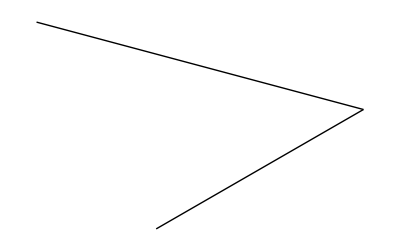

```mathematica
Graphics[
ParseDirectives[{
"t"[30°],"F"[1],"Cart"[-1,1]
}]
]
```